## Problem 9.14

```mathematica
d=5;
R1=5;
R2=-10;
n=1.5;
```

### Part A

```mathematica
(* Answer to part A. Just plug everything into the equation for a thick lens *)
```

```mathematica
ABCDmatrix={{1-d/R1*(1-1/n),d/n},{-(n-1)*(1/R1-1/R2)+d/(R1*R2)*(2-n-1/n),1+d/R2*(1-1/n)}};
ABCDmatrix//MatrixForm
```

(0.666667 | 3.33333
-0.133333 | 0.833333)

### Part B

```mathematica
a=ABCDmatrix[[1]][[1]];
b=ABCDmatrix[[1]][[2]];
c=ABCDmatrix[[2]][[1]];
d=ABCDmatrix[[2]][[2]];
```

```mathematica
(* Answer to Part B *)
```

```mathematica
feff=-1/c
p1=(1-d)/c
p2=(1-a)/c
```

7.5

-1.25

-2.5

## Problem 9.18

```mathematica
(* Set up the lens system as given in the example *)
```

```mathematica
mat1={{1,2*L},{0,1}};
mat2={{1,0},{-1/f,1}};
mat3={{1,2*L},{0,1}};
mat4={{1,0},{-1/f,1}};
```

```mathematica
mat1.mat2.mat3.mat4//MatrixForm
```

(1-(2 L)/f-(2 L+2 L (1-(2 L)/f))/f | 2 L+2 L (1-(2 L)/f)
-1/f-(1-(2 L)/f)/f | 1-(2 L)/f)

```mathematica
(* Define A and D and plug them into Equation 9.73 *)
```

```mathematica
A=1-2*L/f-(2*L+2*L*(1-2*L/f))/f;
De=1-2*L/f;
Simplify[1/2*(A+De)]
stable[L_]:=Simplify[1/2*(1-2*L/f-(2*L+2*L*(1-2*L/f))/f+1-2*L/f)]
```

1-(2 L)/25+L^2/1250

```mathematica
(* Define our f to be 50 cm *)
```

```mathematica
f=50
```

50

```mathematica
(* For -1 *)
```

```mathematica
Solve[1-(2 L)/25+L^2/1250==-1,L]
```

{{L→50},{L→50}}

```mathematica
(* For 1 *)
```

```mathematica
Solve[1-(2 L)/25+L^2/1250==1,L]
```

{{L→0},{L→100}}

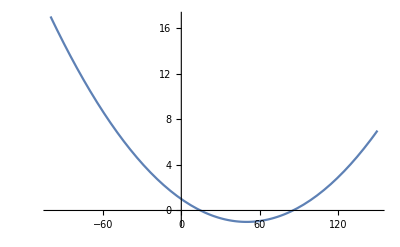

```mathematica
Plot[1-(2 L)/25+L^2/1250,{L,-100,150}]
```

```mathematica
stable[0]
stable[50]
stable[100]
```

1

-1

1

```mathematica
(* Starting at 0, we go from 1 to -1 once we reach 50. That is one stable range. 
Then, we go from -1 to 1 from 50 to 100. That is another stable range. *)
```

## Lab 9.15

```mathematica
Clear[A,B,c,De]
```

```mathematica
(* Data taken from lab *)
```

```mathematica
d01=22;
di1=145.5;
d02=44.5;
di2=45.5;
d03=145;
di3=22.5;
```

```mathematica
(* Plug them into Equation 9.59 *)
```

```mathematica
Equation[x_,y_]:=x*A+B+x*y*c+y*De;
sol1=Equation[d01,di1]
sol2=Equation[d02,di2]
sol3=Equation[d03,di3]
```

22 A+B+3201. c+145.5 De

44.5 A+B+2024.75 c+45.5 De

145 A+B+3262.5 c+22.5 De

```mathematica
(* Get them in terms of D by solving the system of equations *)
```

```mathematica
msolve={-1/145.5*{22,1,3201},-1/45.5*{44.5,1,2024.75},-1/22.5*{145 ,1,3262.5}};
solutions={1,1,1};
answer=Dot[Inverse[msolve], solutions];
answer //MatrixForm //N
```

(1.03263
40.6895
-0.0652632)

```mathematica
(* Use the answers above to get A, B, and C. Then plug them back into 9.59 to get D *)
```

```mathematica
cfinal=finalsol[[3]];
bfinal=finalsol[[2]];
afinal=finalsol[[1]];
dfinal=(22*afinal+bfinal+3201*cfinal)/145.5
```

-1.

```mathematica
(* Use A, B, C, and D to get feff, p1, and p2 *)
```

```mathematica
feff=-1/cfinal
p1=(1-dfinal)/cfinal
p2=(1-afinal)/cfinal
```

15.3226

-30.6452

0.5